# Building Tensor Networks

This tutorial covers the basics of building tensor networks in the Wolfram Language. It begins with the TensorNetwork object itself — what it bundles, how to interrogate it, and what makes the head a distinct value rather than an opaque tagged list. It then walks through the four constructor patterns: tensors plus hyperedges, einsum-style rules with an explicit output specification, conversion from an Inactive TensorContract expression, and a symbolic-skeleton constructor that builds ArraySymbol placeholders from a hypergraph and dimension association alone. The named-topology section uses RandomTensorNetwork to generate instances of the standard families — matrix product states and operators, tensor trains, PEPS on a 2D grid, tree tensor networks, and MERA — including the boundary and field options shared by the chain families. Property dispatch covers the tn["..."] interface and the underlying TensorNetworkData association. Hyperedges and binarization explains the SymbolicDeltaProductArray spider trick that lets pairwise contraction-path algorithms consume otherwise non-binary networks. Edits and transformations cover TensorNetworkAdd, TensorNetworkDelete, TensorNetworkReplaceIndices on the graph form, SparseTensorNetwork, and ToTensorNetworkGraph.

```mathematica
Needs["Wolfram`TensorNetworks`"]
```

## 1. The TensorNetwork object

A tensor network is a collection of tensors wired together by named legs. The fundamental Wolfram-Language container for one is TensorNetwork, with the canonical signature TensorNetwork[tensors, hyperedges, output]. The three pieces of state are a flat list of numeric (or symbolic) tensors, a list of hyperedges — each itself a list of integer leg labels naming the indices that the corresponding tensor exposes — and an output specification controlling which legs survive as free indices after the network is contracted. The output argument is optional; it defaults to Automatic, which keeps exactly the indices that appear in only one tensor (the network's open legs). Any index that appears more than once is treated as contracted.

Conceptually the hyperedges play the role of a hypergraph: each integer label is a vertex of the hypergraph; each inner list is an edge naming the legs of one tensor. The network does not commit to a contraction order. Path search, binarization, and evaluation are all deferred to downstream functions that consume the object — see TensorNetworkContract and OptimalContractionPath.

Prepare two example tensors.

```mathematica
A=RandomReal[1,{2,3}]; 
B=RandomReal[1,{3,4}];
```

Wrap them in a TensorNetwork by passing the tensor list and a hyperedge list. The matrices A and B each have rank 2, so each inner hyperedge list has length 2. The shared label 2 names the joining bond — it appears in both hyperedges and will be contracted away. Labels 1 and 3 each appear exactly once and remain free.

```mathematica
tn=TensorNetwork[{A,B},{{1,2},{2,3}}]
```

TensorNetwork[…]

The head of the resulting expressions is the symbol TensorNetwork itself. The paclet installs a custom summary box, so the object renders as a single compact glyph in the front end rather than unfolding into a screen-filling list of numeric entries. This matters when you start composing operations — the object can be passed around, stored, and combined without ever spilling its tensor data into the output history.

```mathematica
tn["Hypergraph"]
```

-Graphics-

Use TensorNetworkQ to test whether an expression is a valid network. It checks both the head and the structural invariants (lengths agree, every hyperedge length equals the rank of its tensor, every output leg is a label that actually appears). Predicates of this form are useful as guards inside PatternTest constructions.

```mathematica
TensorNetworkQ[tn]
```

True

The free indices are the ones that appear in exactly one hyperedge — the network's open legs. When the output specification is Automatic, the free-index list is computed automatically by counting label occurrences. The next section shows how to override that to expose contracted legs or to scalar-out.

```mathematica
tn["FreeIndices"]
```

{1,3}

## 2. Constructor forms

There are four idiomatic ways to construct a network. The first three start from existing tensors — either fully numeric or carrying symbolic entries — and differ only in the syntax used to attach them to a hypergraph. The fourth bypasses tensors entirely: you describe the shape of the network with a hypergraph and a dimension association, and the constructor populates each slot with an ArraySymbol placeholder of the correct rank and dimensions. The symbolic form is useful for planning a contraction before the numerics exist, for index-only analyses, and for testing path search under specific shape regimes.

### 2.1. Tensors plus a hyperedge list

Form 1: tensors plus a hyperedge list. Each inner list is one hyperedge, naming the legs it joins. The constructor matches the leg names to tensor ranks in order — the kth label inside the ith hyperedge corresponds to the kth axis of the ith tensor. Shapes must match: if the same label appears twice, the two corresponding tensor axes must have the same dimension.

```mathematica
tn1=TensorNetwork[{A,B},{{1,2},{2,3}}]
```

TensorNetwork[…]

```mathematica
tn1["Hypergraph"]
```

-Graphics-

```mathematica
{tn1["Hyperedges"],tn1["FreeIndices"]}
```

{{{1,2},{2,3}},{1,3}}

### 2.2. Einsum-style with explicit output

Form 2: einsum-style with an explicit hyperedges -> output rule. The right-hand side lists which indices survive as free legs after contraction. Setting it equal to the indices that appear once recovers Automatic behavior; setting it to {} contracts the network to a scalar (a tensor trace); setting it to a permutation of the auto-free list reorders the output axes. This is the form most directly cognate with einsum strings in NumPy or with ITensor's index-naming conventions.

```mathematica
tn2=TensorNetwork[{A,B},{{1,2},{2,3}}->{1,3}]
```

TensorNetwork[…]

### 2.3. Inactive TensorContract expression

Form 3: lift an unevaluated TensorContract expression. The contraction is written in the native TensorProduct / TensorContract notation Wolfram Language uses for higher-rank tensor algebra; the Inactive wrapper keeps it from evaluating eagerly. This is the natural bridge from a mathematical description of a contraction into network form — the inactive expression carries enough information to recover both the tensors and the contracted axis pairs, and the constructor reads it directly.

```mathematica
tn3=TensorNetwork[Inactive[TensorContract][Inactive[TensorProduct][A,B],{{2,3}}]]
```

TensorNetwork[…]

### 2.4. Symbolic skeleton from hypergraph

Form 4: build a symbolic skeleton from the hypergraph alone. The first argument is the hyperedge list (optionally with an output spec); the second is an association mapping each leg label to its dimension. Tensors are filled in with ArraySymbol of the correct shape, all bearing the same formal symbol so they are clearly placeholders. Use this when the hypergraph topology is fixed but the entries are not — for symbolic manipulations, scaling analyses, or as a template that InitializeTensorNetwork can later populate with real values.

Symbolic tensor networks with global contractions slots and final output:

```mathematica
tn4=TensorNetwork[{{1,2},{2,3}}->{3,1}]
```

TensorNetwork[…]

Corresponding tensors:

```mathematica
tn4["Tensors"]
```

{T2dd,T2dd}

Corresponding index dimensions (symbolic only):

```mathematica
tn4["Dimensions"]
```

{{d,d},{d,d}}

Symbolic tensor networks with contractions slots, final output and a specific glorbal-index dimensions:

```mathematica
tn5=TensorNetwork[{{1,2},{2,3}}->{1,3},<|1->2,2->5,3->4|>]
```

TensorNetwork[…]

Show tensor dimensions:

```mathematica
tn5["Dimensions"]
```

{{2,5},{5,4}}

### 2.5. Dimension list instead of association

When indices have not yet been bound to arrays, the hypergraph constructor also accepts a positional _List of dimensions in place of an Association. The dimensions are paired with the union of integer index labels in sorted order: the first dimension is assigned to the smallest index, the second to the next, and so on. This is the most compact way to specify a symbolic skeleton when you do not care about index names.

```mathematica
TensorNetwork[{{1,2},{2,3}}->{1,3},{2,3,4}]
```

TensorNetwork[…]

Verify the dimension mapping via ["Dimensions"]: indices 1, 2, 3 receive dimensions 2, 3, 4 respectively.

```mathematica
TensorNetwork[{{1,2},{2,3}}->{1,3},{2,3,4}]["Dimensions"]
```

{{2,3},{3,4}}

### 2.6. Output permutation via Cycles

The third argument of TensorNetwork accepts either an explicit list of free indices, or a Cycles permutation that is applied to the auto-derived free-index order. The Cycles form is convenient when you want to keep the default selection of free indices but reorder them — for instance, when downstream code expects rows before columns rather than the order in which they happened to appear in the hyperedge list.

```mathematica
A=RandomReal[1,{2,3}]; 
B=RandomReal[1,{3,4}];
```

```mathematica
tnPerm=TensorNetwork[{A,B},{{1,2},{2,3}},Cycles[{{1,2}}]]
```

TensorNetwork[…]

The default free-index order would have been {1, 3}. Applying the cycle (1 2) swaps the two positions, giving {3, 1}.

```mathematica
tnPerm["FreeIndices"]
```

{3,1}

### 2.7. Round-trip from an annotated graph

The constructor also accepts an annotated Graph whose vertices carry tensors and indices as annotations — in other words, anything satisfying TensorNetworkGraphQ. This is the inverse of ToTensorNetworkGraph: starting from a flat TensorNetwork[…], round-tripping through the graph form and back recovers a flat object with the same tensors and the same contraction pattern. The integer index labels are replaced by structured Superscript/Subscript labels that record edge direction, but the underlying bond pattern is unchanged.

```mathematica
base=TensorNetwork[{A,B},{{1,2},{2,3}}]
```

TensorNetwork[…]

```mathematica
TensorNetworkData@base
```

<|Tensors→{{{0.92579,0.327791,0.458629},{0.267579,0.411054,0.0854018}},{{0.726854,0.043862,0.724771,0.73795},{0.765395,0.572407,0.445793,0.61895},{0.768739,0.726334,0.683203,0.764582}}},Dimensions→{{2,3},{3,4}},Hyperedges→{{1,2},{2,3}},Indices→{{1^1,1^2},{2^2,2^3}},Vertices→{1,2},Bonds→{{1^2,2^2}→3},Contractions→{{1^1,{1^2,2^2}},{{1^2,2^2},2^3}},ContractionIndices→{{1,2},{2,3}},FreeIndices→{1,3}|>

```mathematica
base["Hypergraph"]
```

-Graphics-

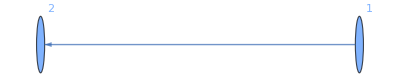

```mathematica
g=ToTensorNetworkGraph[base]
```

```mathematica
roundTrip=TensorNetwork[g]
```

TensorNetwork[…]

```mathematica
TensorNetworkData@roundTrip
```

<|Tensors→{{{0.92579,0.327791,0.458629},{0.267579,0.411054,0.0854018}},{{0.726854,0.043862,0.724771,0.73795},{0.765395,0.572407,0.445793,0.61895},{0.768739,0.726334,0.683203,0.764582}}},Dimensions→{{2,3},{3,4}},Hyperedges→{{1^1,1^2},{1^2,2_2}},Indices→{{1^(1^1),1^(1^2)},{2^(1^2),2^(2_2)}},Vertices→{1,2},Bonds→{{1^(1^2),2^(1^2)}→3},Contractions→{{1^(1^1),{1^(1^2),2^(1^2)}},{{1^(1^2),2^(1^2)},2^(2_2)}},ContractionIndices→{{1^1,1^2},{1^2,2_2}},FreeIndices→{1^1,2_2}|>

For purely string-driven index notation (the einsum DSL), see EinsteinSummation and IndexedMultiply; the former produces an Inactive[TensorContract][…] expression that section 2.3 ingests directly.

## 3. Named topologies

Most networks used in physics and machine learning have stylized topologies — chains, trees, grids, or hierarchical layers — for which the paclet ships dedicated random constructors. The driver is RandomTensorNetwork. Each family is specified as a head bearing the topology name with parameters in positional form: "MPS"[L, D, d] for an open matrix product state of length L, bond dimension D, and physical (site) dimension d. Family-specific options follow as standard Rules. The tensor entries are drawn from a Gaussian distribution by default; the Method option selects real or complex sampling.

### 3.1. Matrix product states

An MPS on four sites with bond dimension 2 and physical dimension 2. The two boundary sites have rank 2 (one bond, one physical leg); the two interior sites have rank 3 (left bond, right bond, physical). Set SeedRandom first to make the construction reproducible.

```mathematica
SeedRandom[42];
```

```mathematica
mps=RandomTensorNetwork["MPS"[4,2,2]]
```

TensorNetwork[…]

```mathematica
mps["Hypergraph"]
```

-Graphics-

Inspect the hyperedge structure. Each contracted bond appears as a shared label between neighboring sites — labels 1, 2, and 3 link successive pairs. The physical legs (labels 5 through 8) appear only once each and remain free.

```mathematica
mps["Hyperedges"]
```

{{1,5},{1,2,6},{2,3,7},{3,8}}

```mathematica
mps["Dimensions"]
```

{{2,2},{2,2,2},{2,2,2},{2,2}}

### 3.2. Tensor trains

A tensor train ("TT") is structurally an MPS without a physical dimension — useful for compressing arbitrary high-rank tensors as a chain of low-rank cores. The chain shape is the same (left bond, right bond per interior core) but every tensor lacks the physical leg. Compare the hyperedges: a 4-site tensor train has only the bond indices and no site labels.

```mathematica
tt=RandomTensorNetwork["TT"[6,3]]
```

TensorNetwork[…]

```mathematica
tt["Hypergraph"]
```

-Graphics-

```mathematica
tt["Hyperedges"]
```

{{1},{1,2},{2,3},{3,4},{4,5},{5}}

```mathematica
tt["Dimensions"]
```

{{3},{3,3},{3,3},{3,3},{3,3},{3}}

### 3.3. Matrix product operators

A matrix product operator ("MPO") doubles the physical legs — one ket-side and one bra-side per site, so that the object represents an operator rather than a state. Each interior tensor has rank 4 (two bond legs plus two physical legs); each boundary tensor has rank 3. The free-index list interleaves the ket and bra indices in pairs.

```mathematica
mpo=RandomTensorNetwork["MPO"[4,2,2]]
```

TensorNetwork[…]

```mathematica
mpo["Hypergraph"]
```

-Graphics-

```mathematica
mpo["FreeIndices"]
```

{5,9,6,10,7,11,8,12}

### 3.4. PEPS on a 2D grid

PEPS — projected entangled pair states — lives on a 2D grid. The first argument is {rows, cols}. Each site has up to four bond legs (one to each grid neighbor) plus a single physical leg; boundary and corner sites have correspondingly fewer bonds. The labeling encodes the (row, column) coordinates and the physical-leg range in separate integer bands (hundreds for rows, thousands for physical legs in this example) so the resulting hyperedge list stays readable.

```mathematica
peps=RandomTensorNetwork["PEPS"[{2,2},2,2]]
```

TensorNetwork[…]

```mathematica
peps["Hypergraph"]
```

-Graphics-

### 3.5. Tree tensor networks

Tree tensor networks ("TTN") build hierarchical topologies — bonds branch outward from a single root through successive layers, with no horizontal connections between siblings. They naturally represent states with a coarse-graining structure and are common in chemistry-oriented TN methods. Specify depth (number of layers from root to leaves), bond dimension, and branching (number of children per node).

```mathematica
ttn=RandomTensorNetwork["TTN"[2,2,2]]
```

TensorNetwork[…]

```mathematica
ttn["Hypergraph"]
```

-Graphics-

### 3.6. MERA

The multi-scale entanglement renormalization ansatz ("MERA") adds horizontal disentanglers between layers of a tree, giving the network a characteristic causal-cone structure that captures critical scaling well. Specify width (number of physical sites), bond dimension, and layers (renormalization depth).

```mathematica
mera=RandomTensorNetwork["MERA"[4,2,2]]
```

TensorNetwork[…]

```mathematica
mera["Hypergraph"]
```

-Graphics-

### 3.7. Boundary and field options

Chain families accept the boundary option "Boundary" -> "Open" (default — the leftmost and rightmost sites have rank 2) or "Periodic" — the latter wraps the last site back to the first, adding one extra hyperedge and making every site interior-shaped. All families accept Method -> "Complex" to populate tensors with complex Gaussian entries instead of real ones; the underlying distribution becomes the standard complex normal, and downstream contractions remain complex throughout.

```mathematica
mpsP=RandomTensorNetwork["MPS"[4,2,2],"Boundary"->"Periodic"]
```

TensorNetwork[…]

```mathematica
mpsP["Hypergraph"]
```

-Graphics-

```mathematica
mpsP["Hyperedges"]
```

{{1,2,5},{2,3,6},{3,4,7},{4,1,8}}

```mathematica
mpsC=RandomTensorNetwork["MPS"[3,2,2],Method->"Complex"]
```

TensorNetwork[…]

### 3.8. Random networks on arbitrary graphs

Outside the named topology families, RandomTensorNetwork accepts any Graph object (anything satisfying GraphQ), or an {n, m} shortcut that expands to RandomGraph[{n, m}]. Each graph vertex becomes a tensor; each graph edge becomes a contracted bond. The dimension argument has three forms, and an optional third argument controls how many additional free legs each vertex carries beyond its graph degree.

Three forms are available:
  • RandomTensorNetwork[g, maxDim] — each index gets an independent random dimension in {2, maxDim}.
  • RandomTensorNetwork[g, {fixedDim}] — every index has the same dimension fixedDim.
  • RandomTensorNetwork[g, dimSpec, additionalRank] — each vertex's rank is sampled from {VertexDegree[v], VertexDegree[v] + additionalRank}, and the extra legs become free indices.

The Method -> "Complex" option draws the tensor entries from a complex distribution rather than the default real one. This is the standard form used to generate inputs for contraction-path benchmarks — see GreedyContractionPath and OptimalContractionPath.

A 5-vertex, 8-edge random graph with dimensions up to 3:

```mathematica
SeedRandom[42]; 
tnA=RandomTensorNetwork[{5,8},3]
```

TensorNetwork[…]

```mathematica
tnA["Size"]
```

5

Fixed dimension 2 on every index:

```mathematica
tnB=RandomTensorNetwork[gr=RandomGraph[{6,10}],{2}]
```

TensorNetwork[…]

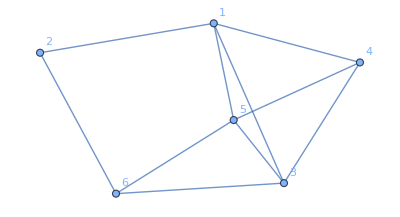

```mathematica
Graph[gr,VertexLabels->Automatic]
```

```mathematica
Union@Catenate@tnB["Dimensions"]
```

{2}

Adding additionalRank -> 2 gives each vertex between VertexDegree[v] and VertexDegree[v] + 2 legs; the surplus become free indices, useful when generating networks with prescribed free-leg counts:

```mathematica
tnC=RandomTensorNetwork[RandomGraph[{4,6}],3,2]
```

TensorNetwork[…]

```mathematica
tnC["Dimensions"]
```

{{2,2,3,3,3},{3,3,3,2},{3,2,2,3,2},{2,2,2,2}}

```mathematica
tnC["FreeIndices"]
```

{1,5,7,11,12,16,18}

## 4. Property dispatch

Every property of a network is reached through the same dispatch syntax: tn["PropertyName"]. This keeps the surface API small — there is no separate TensorNetworkXyz accessor function for each field. The same property names appear inside the full data association returned by TensorNetworkData, so you can either pick off one field at a time or grab everything in one call. The dispatch is implemented as a downvalue on the TensorNetwork head and is therefore extensible from outside the paclet if you need to attach your own derived quantities.

```mathematica
tnD=RandomTensorNetwork["MPS"[3,2,2]]
```

TensorNetwork[…]

"Tensors" returns the raw tensor list — three elements for this 3-site MPS. The list is the same object that was passed to the constructor (or that the random generator produced); it round-trips exactly. "Hyperedges" returns the integer labelling of the bonds in the same order.

```mathematica
Length[tnD["Tensors"]]
```

3

```mathematica
tnD["Hyperedges"]
```

{{1,4},{1,2,5},{2,6}}

"FreeIndices" names the open legs — the indices that survive the contraction. "Dimensions" returns one list per tensor giving the size of each of its legs, parallel to the hyperedge list. Together these are enough to predict the shape of the contracted result without actually running the contraction.

```mathematica
{tnD["FreeIndices"],tnD["Dimensions"]}
```

{{4,5,6},{{2,2},{2,2,2},{2,2}}}

"Indices" returns a typed view: each leg becomes a Superscript carrying both its tensor identifier and its hyperedge label, of the form Superscript[tensor, edge]. This is the form that downstream graph-level operations like TensorNetworkReplaceIndices consume — the typed wrapper disambiguates which copy of a shared label you mean when the same integer appears as a leg of more than one tensor.

```mathematica
tnD["Indices"]
```

{{1^1,1^4},{2^1,2^2,2^5},{3^2,3^6}}

"Bonds" enumerates the contracted edges and the dimension each one carries. Each bond is reported as a rule from a pair of typed indices to a dimension, which makes it easy to scan a network and sanity-check that adjacent tensors agree on the dimensions of shared legs before contraction. A mismatch in this output is always the cause of a downstream evaluation error.

```mathematica
tnD["Bonds"]
```

{{1^1,2^1}→2,{2^2,3^2}→2}

Two boolean flags summarize the network's structural state. "BinaryQ" is True when every index appears in at most two tensors — i.e. the network is a pure (multi)graph, not a true hypergraph. "SparseQ" reports whether every tensor is a SparseArray. These two predicates control which fast paths the contraction engine can take: binary networks can be fed directly into a pairwise path search, and sparse networks use SparseArray-aware tensor algebra throughout.

```mathematica
{tnD["BinaryQ"],tnD["SparseQ"]}
```

{True,False}

"Graph" returns the network as a Graph object — tensors and bond-spiders as vertices, leg connections as directed edges. It is the form used by visualization, path-search, and structural-edit code paths. The graph is bipartite in spirit (tensor vertices vs. spider vertices), with edges directed from the spider toward each connected tensor leg.

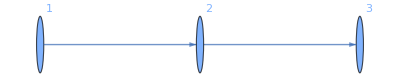

```mathematica
tnD["Graph"]
```

Enumerate every property the dispatch knows about with tn["Properties"]. The list includes both the raw fields and several derived views ("Hypergraph", "Vertices", "Ranks"). Use this as a discoverability handle when exploring a new network.

```mathematica
tnD["Properties"]
```

{Tensors,Hyperedges,FreeIndices,Hypergraph,Dimensions,Ranks,Indices,IndexDimensions,Vertices,Bonds,Contractions,ContractionIndices,BinaryQ,SparseQ,Graph,GraphData,Data}

TensorNetworkData gives back the full underlying association in one call. Use it for serialization, for writing functions that walk every field at once, or when you want to grab several properties without paying the dispatch overhead per access.

```mathematica
TensorNetworkData[tnD]
```

<|Tensors→{{{-0.454139,0.278953},{0.987086,-0.303296}},{{{-0.148158,0.198091},{0.354684,0.0390127}},{{-0.0277439,0.672699},{-0.743107,-0.827894}}},{{-0.985543,0.978814},{0.0249221,-0.976514}}},Dimensions→{{2,2},{2,2,2},{2,2}},Hyperedges→{{1,4},{1,2,5},{2,6}},Indices→{{1^1,1^4},{2^1,2^2,2^5},{3^2,3^6}},Vertices→{1,2,3},Bonds→{{1^1,2^1}→2,{2^2,3^2}→2},Contractions→{{{1^1,2^1},1^4},{{1^1,2^1},{2^2,3^2},2^5},{{2^2,3^2},3^6}},ContractionIndices→{{1,4},{1,2,5},{2,6}},FreeIndices→{4,5,6}|>

### 4.1. Function form vs property form

For every key dispatched through tn["Key"] there is a standalone function with the same name. Both forms return identical results and share an implementation — the property form just forwards to the function. Pick whichever reads cleaner at the call site: the property form is concise when the network is already in hand; the function form composes naturally with Map, @*, and other higher-order operators.

Property form | Function form
tn["Tensors"] | TensorNetworkTensors[tn]
tn["Size"] | TensorNetworkSize[tn]
tn["FreeIndices"] | TensorNetworkFreeIndices[tn]
tn["Indices"] | TensorNetworkIndices[tn]
tn["IndexDimensions"] | TensorNetworkIndexDimensions[tn]
tn["Contractions"] | TensorNetworkContractions[tn]
tn["GraphData"] | TensorNetworkGraphData[tn]
tn["Data"] | TensorNetworkData[tn]

The two pairings agree on the values they return:

```mathematica
A=RandomReal[1,{2,3}]; B=RandomReal[1,{3,4}];
```

```mathematica
tn=TensorNetwork[{A,B},{{1,2},{2,3}}]
```

TensorNetwork[…]

```mathematica
tn["Size"]==TensorNetworkSize[tn]
```

True

```mathematica
tn["FreeIndices"]===TensorNetworkFreeIndices[tn]
```

True

## 5. Hyperedges and binarization

A hyperedge is an index that joins three or more tensors at once. In ordinary tensor diagrams every edge connects exactly two tensors, but the underlying mathematics — sums over a shared dummy index — is happy to admit any arity. Hyperedges express copy and broadcast structure that two-end edges cannot draw, and they appear naturally in symmetry-restricted networks, in tensor decompositions like CP, and whenever a delta-function constraint couples more than two tensors.

Hyperedges are perfectly legal as inputs to TensorNetwork, but most contraction-path search algorithms assume pairwise contractions, so the paclet provides a transformation step that binarizes a hyperedge network into an equivalent network with only two-end edges. The trick is to attach a small auxiliary tensor — a Kronecker-delta "spider" — to each hyperedge: the spider replaces the n-ary constraint with one extra vertex wired pairwise to each tensor that previously shared the hyperedge. The resulting network has more tensors but pure binary topology.

Build three tensors sharing index 2 — a genuine hyperedge.

```mathematica
T1=RandomReal[1,{2,3}]; T2=RandomReal[1,{3,4}]; T3=RandomReal[1,{3,5}];
```

```mathematica
hyperTN=TensorNetwork[{T1,T2,T3},{{1,2},{2,3},{2,4}}]
```

TensorNetwork[…]

BinaryTensorNetworkQ confirms the network is not binary: the label 2 appears in three tensors, so at least one index occurs more than twice. Any network that hits this case will be rejected by purely pairwise path-search code unless it is preprocessed.

```mathematica
BinaryTensorNetworkQ[hyperTN]
```

False

Applying BinaryTensorNetwork performs the binarization. It inserts a SymbolicDeltaProductArray spider on the offending hyperedge — a small auxiliary tensor whose entries enforce the equality constraint that the original hyperedge encoded. The spider replaces the n-ary connection with one extra vertex wired to each original leg by its own two-end edge. The network now has 4 tensors, only pairwise connections, and passes BinaryTensorNetworkQ.

```mathematica
bin=BinaryTensorNetwork[hyperTN]
```

TensorNetwork[…]

```mathematica
{Length[bin["Tensors"]],Head[bin["Tensors"][[-1]]],BinaryTensorNetworkQ[bin]}
```

{4,SymbolicDeltaProductArray,True}

The arrow notation 1 -> 2 in the new hyperedge list denotes the rewritten leg name: it reads as "the copy of the old index 2 that hangs off tensor 1." Each original tensor keeps one of these distinguished names instead of the shared label, and the new delta tensor connects them all. The naming is a record of where the spider came from.

```mathematica
bin["Hyperedges"]
```

{{1,1→2},{2→2,3},{3→2,4},{1→2,2→2,3→2}}

High-level contraction code applies this transformation automatically — OptimalContractionPath and TensorNetworkContract both call BinaryTensorNetwork internally on non-binary input, so you rarely need to invoke it directly. Knowing what it does, however, makes the resulting paths legible: every spider in the output trace is one of these inserted vertices, not a tensor from the original network.

## 6. Edits and transformations

Networks are immutable values: transformations return new networks rather than mutating in place. The paclet exposes a small set of structural edits — adding and deleting tensors, renaming indices — plus one bulk storage conversion to sparse representation, and one accessor that returns the network in its annotated-graph form for use with the full Graph API. The edits compose freely: every transformation accepts a TensorNetwork and produces a fresh TensorNetwork (or, where noted, a Graph form), so longer-running pipelines can be built by chaining them with ReplaceAll or Composition.

### 6.1. Adding and deleting tensors

TensorNetworkAdd attaches a new tensor to an existing network. Supply the network, the tensor, and the list of leg labels the tensor should be wired to. Any label that already exists in the network becomes a shared bond, contracting the new tensor with whatever already used it; labels that are new become additional free indices. The rank of the new tensor must match the length of its leg-label list, and shared labels must agree on dimension.

```mathematica
base=TensorNetwork[{A,B},{{1,2},{2,3}}]
```

TensorNetwork[…]

```mathematica
Cmat=RandomReal[1,{4,5}]; 
added=TensorNetworkAdd[base,Cmat,{3,4}]
```

TensorNetwork[…]

```mathematica
{added["Hyperedges"],added["FreeIndices"]}
```

{{{1,2},{2,3},{3,4}},{1,4}}

TensorNetworkDelete removes a tensor by its position in the tensor list. Any leg that was previously contracted only through the deleted tensor becomes free — the bond is broken, and the remaining tensor's leg with that label now appears in only one hyperedge. The free-index list reflects the new topology, so the network is still in a consistent state.

```mathematica
deleted=TensorNetworkDelete[added,2]
```

TensorNetwork[…]

```mathematica
deleted["Hyperedges"]
```

{{1,2},{3,4}}

### 6.2. Renaming indices on the graph form

TensorNetworkReplaceIndices renames legs. It operates on the ToTensorNetworkGraph form, which carries typed indices as vertex annotations — a leg of tensor i bearing label k is stored as i^k. The replacement rules are applied at vertex annotation level, so you pass rules whose left-hand sides are the typed index forms returned by tn["Indices"]. Below, both legs of tensor 1 are renamed to string labels.

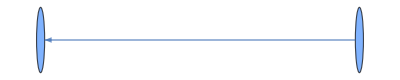

```mathematica
g0=ToTensorNetworkGraph[base]; g1=TensorNetworkReplaceIndices[g0,{1^1->"a",1^2->"b"}]
```

```mathematica
AnnotationValue[{g1,1},"Index"]
```

{a,b}

### 6.3. Sparse storage

SparseTensorNetwork converts every tensor in the network to SparseArray form. The hypergraph and indices are preserved exactly; only the storage representation of the tensor entries changes. This is useful before evaluating contractions on highly sparse or structured tensors — the contraction engine has fast paths for SparseArray inputs that avoid materializing dense intermediates.

```mathematica
sparseTN=SparseTensorNetwork[base]
```

TensorNetwork[…]

```mathematica
{sparseTN["SparseQ"],Head[sparseTN["Tensors"][[1]]]}
```

{True,SparseArray}

### 6.4. The annotated graph form

Finally, ToTensorNetworkGraph returns the network as an annotated Graph object. The graph form carries tensors as vertex annotations, bonds as labelled directed edges, and indices as both vertex and edge annotations. Because it is a genuine Graph, it accepts the full graph API — you can call VertexList, EdgeList, GraphPlot, run graph algorithms, and visualize the topology. Several transformations including TensorNetworkReplaceIndices consume this form directly. Use TensorNetworkGraphData to extract the same property association as TensorNetworkData from the graph form, and TensorNetworkGraphQ to test for it.

## 7. Cycles and visualizations

Two transformations that operate on the annotated graph form fall outside the basic edit-and-rename workflow of section 6: cycle breaking and index-connectivity extraction. Cycle breaking is required whenever a network contains a closed loop — for instance, a chain with periodic boundary conditions — because sequential pairwise contraction cannot reduce a cycle without first opening it. Index-connectivity extraction collapses the network down to its bond structure alone, useful for inspecting how indices share tensors without the data getting in the way.

### 7.1. Breaking cycles with TensorNetworkRemoveCycles

A directed-graph tensor network with a cycle (for example, three rank-2 tensors wired 1 → 2 → 3 → 1) cannot be reduced by sequential pairwise contraction without first being broken. TensorNetworkRemoveCycles walks the cycle list and, for each cycle, inserts a cup-and-cap pair of identity tensors: the cup duplicates one bond at the start of the loop and the cap closes the duplicate at the end. The resulting acyclic graph contracts to exactly the same tensor (or scalar) as the closed-loop original because the inserted identities act as the trace that the cycle was already implicitly performing. This is the internal mechanism that makes "Boundary" -> "Periodic" MPS, MPO, and PEPS networks sequentially contractible.

Build a cyclic three-tensor network manually as an annotated directed Graph. Each vertex carries a 2×2 matrix and exposes two indices; the three directed edges close the loop.

```mathematica
M1=RandomReal[1,{2,2}]; M2=RandomReal[1,{2,2}]; M3=RandomReal[1,{2,2}];
```

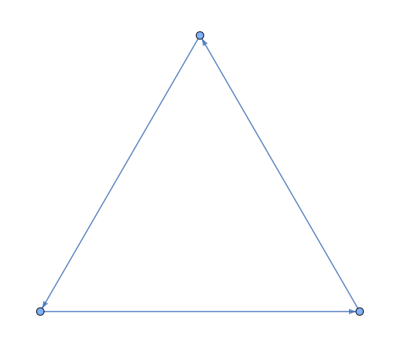

```mathematica
cyclic=Graph[{1,2,3},{DirectedEdge[1,2,{Superscript[1,2],Subscript[2,1]}],DirectedEdge[2,3,{Superscript[2,2],Subscript[3,1]}],DirectedEdge[3,1,{Superscript[3,2],Subscript[1,1]}]},AnnotationRules->{1->{"Tensor"->M1,"Index"->{Subscript[1,1],Superscript[1,2]}},2->{"Tensor"->M2,"Index"->{Subscript[2,1],Superscript[2,2]}},3->{"Tensor"->M3,"Index"->{Subscript[3,1],Superscript[3,2]}}}]
```

The graph reports a non-trivial cycle:

```mathematica
FindCycle[cyclic,Infinity,1]
```

{{12{1^2,2_1},23{2^2,3_1},31{3^2,1_1}}}

After cycle removal the graph is acyclic and FindCycle returns the empty list. Two extra vertices (the cup and the cap) have been inserted:

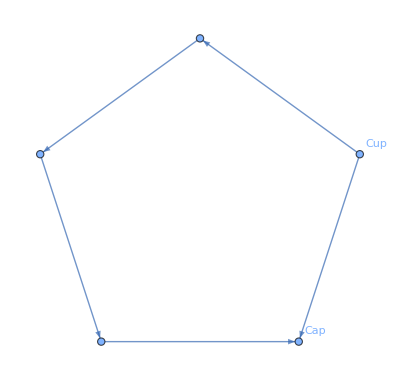

```mathematica
acyclic=TensorNetworkRemoveCycles[cyclic]
```

```mathematica
{FindCycle[acyclic,Infinity,1], VertexCount[acyclic]}
```

{{},5}

### 7.2. Index-connectivity graph

TensorNetworkIndexGraph extracts a separate graph in which the vertices are the indices of the network and an edge joins two indices whenever they appear together on the same tensor. The tensor data is dropped; only the index-incidence structure survives. This is the useful diagram for planning a contraction order, spotting fully-connected clusters, or debugging which tensors share which bonds when the data itself is not interesting.

Pull the index graph off an MPS:

```mathematica
mps=RandomTensorNetwork["MPS"[4,2,2]]
```

TensorNetwork[…]

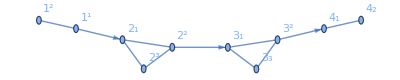

```mathematica
TensorNetworkIndexGraph[mps["Graph"]]
```

Related Guides

TensorNetworks

Related Tech Notes

Tensor Networks Overview

Contraction Paths and Execution

Matrix Product States

## Metadata

### Categorization

Tech Note

Wolfram/TensorNetworks

Wolfram`TensorNetworks`

Wolfram/TensorNetworks/tutorial/BuildingTensorNetworks

### Keywords

tensor network construction, MPS, PEPS, MERA, hyperedge, property dispatch, binarization